```mathematica
A=1.660539 10^-27;
ma=6.015122 A;
mi=170.936323 A;
ωs=2π 320000;
C4= 1.121 10^-56;
C6=2.804 10^-75;
ℏ=1.054571817 10^-34;
mu2=(ma mi)/(ma+mi)
mu=Sqrt[ma/mi]
thetaC = ArcTan[mu];
aho=Sqrt[ℏ/(ωs mi)]
```

9.64881×10^-27

0.187588

1.35935×10^-8

H_ad/ℏω=-1/(2μ R^2)∂^2/(∂θ^2)+1/2μ R^2 cos^2 θ

-1/(2μ R^2)(∂^2 Φ)/(∂θ^2)+1/2μ R^2 cos^2 θ Φ-U Φ=0

1/(2μ R^2)(∂^2 Φ)/(∂θ^2)-1/4 μ R^2(1+cos(2θ) Φ+U Φ=0

(∂^2 Φ)/(∂θ^2)-2μ R^2 1/4 μ R^2(1+cos(2θ) Φ+2μ R^2 U Φ=0

(∂^2 Φ)/(∂θ^2)+(2μ R^2 U-1/2(μ R^2)^2 -1/2(μ R^2)^2 cos (2θ))Φ=0

The Mathieu equation is: y''+(a-2q cos(2z))y=0.

We set q=1/4 μ^2 R^4, or, √(4q)=μ R^2and a(q)=2μ R^2 U-1/2(μ R^2)^2=4 √q U-2q

4 √q U-2q=a(q)

U=(a(q)+2q)/(4 √q)

So the solution to the noninteracting problem are Mathieu functions, which are periodic with period 2π n when a(q) is given by its characteristic value (use A for the even function and B for the odd function):

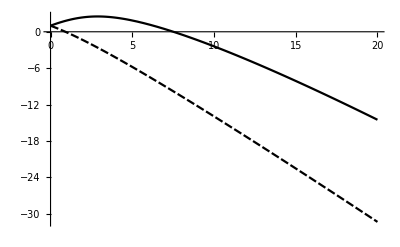

```mathematica
Plot[{MathieuCharacteristicA[1,q],MathieuCharacteristicB[1,q]},{q,0,20}]
```

```mathematica
NIEvenEnergy[n_,mass_,R_]:=Module[{q,a,U,f},
q=1/4 mass^2 R^4;
a=MathieuCharacteristicA[n,q];
U=(a+2q)/(4 √q);
U
]
```

```mathematica
NIOddEnergy[n_,mass_,R_]:=Module[{q,a,U,f},
q=1/4 mass^2 R^4;
a=MathieuCharacteristicB[n,q];
U=(a+2q)/(4 √q);
U
]
```

```mathematica
EvenPotCurves=Table[Table[{R,NIEvenEnergy[n,mu,R]},{R,0.5,50,0.1}],{n,0,10}];
```

```mathematica
OddPotCurves=Table[Table[{R,NIOddEnergy[n,mu,R]},{R,0.5,50,0.1}],{n,1,10}];
```

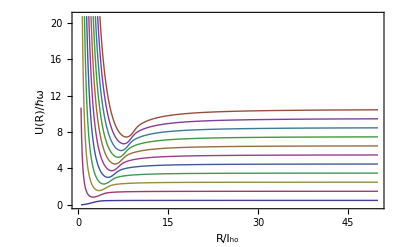

```mathematica
pEven=ListPlot[EvenPotCurves,Joined->True,PlotMarkers->None,PlotTheme->None,Frame->True,LabelStyle->Medium,FrameLabel->{"R/l_ho","U(R)/ℏω"}]
```

```mathematica
Import["/Users/niravmehta/Documents/Code/Nchannel/NDEigenSystem.nb"]
```

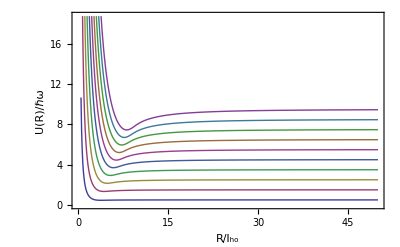

```mathematica
pOdd=ListPlot[OddPotCurves,Joined->True,PlotMarkers->None,PlotTheme->None,Frame->True,LabelStyle->Medium,FrameLabel->{"R/l_ho","U(R)/ℏω"}]
```

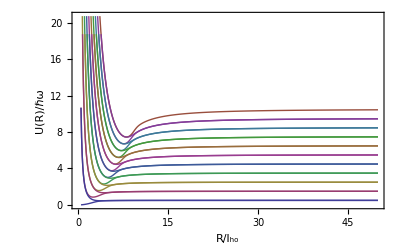

```mathematica
Show[pEven,pOdd]
```

```mathematica
Π=1;Πx=-1;Πy=-1;FullSimplify[{Sin[2m t]-Πx Sin[2m(π- t)],Sin[2m t]-Πy Sin[-2m t],Sin[2m t]-Π Sin[2m(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
FullSimplify[{Cos[2m t]-Πx Cos[2m(π- t)],Cos[2m t]-Πy Cos[-2m t],Cos[2m t]-Π Cos[2m(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
```

{0,0,0}

{2 Cos[2 m t],2 Cos[2 m t],0}

```mathematica
Π=1;Πx=1;Πy=1;FullSimplify[{Sin[2m t]-Πx Sin[2m(π- t)],Sin[2m t]-Πy Sin[-2m t],Sin[2m t]-Π Sin[2m(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
FullSimplify[{Cos[2m t]-Πx Cos[2m(π- t)],Cos[2m t]-Πy Cos[-2m t],Cos[2m t]-Π Cos[2m(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
```

{2 Sin[2 m t],2 Sin[2 m t],0}

{0,0,0}

```mathematica
Π=-1;Πx=-1;Πy=1;FullSimplify[{Sin[(2m+1) t]-Πx Sin[(2m+1)(π- t)],Sin[(2m+1) t]-Πy Sin[-(2m+1) t],Sin[(2m+1) t]-Π Sin[(2m+1)(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
FullSimplify[{Cos[(2m+1) t]-Πx Cos[(2m+1)(π- t)],Cos[(2m+1) t]-Πy Cos[-(2m+1) t],Cos[(2m+1) t]-Π Cos[(2m+1)(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
```

{2 Sin[t+2 m t],2 Sin[t+2 m t],0}

{0,0,0}

```mathematica
Π=-1;Πx=1;Πy=-1;FullSimplify[{Sin[(2m+1) t]-Πx Sin[(2m+1)(π- t)],Sin[(2m+1) t]-Πy Sin[-(2m+1) t],Sin[(2m+1) t]-Π Sin[(2m+1)(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
FullSimplify[{Cos[(2m+1) t]-Πx Cos[(2m+1)(π- t)],Cos[(2m+1) t]-Πy Cos[-(2m+1) t],Cos[(2m+1) t]-Π Cos[(2m+1)(t+π)]},Assumptions->{m∈Integers,t∈Reals}]
```

{0,0,0}

{2 Cos[t+2 m t],2 Cos[t+2 m t],0}

### Check numerical (fortran) noninteracting curves

For the “01” fortran case that has zero value at θ=0 and zero derivative at θ=π/2

```mathematica
RawVEff=Transpose[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/QuickEffV.dat"]];
```

```mathematica
Veff0:=Interpolation[Transpose[{RawVEff[[1]],RawVEff[[2]]}]]
```

{R→1.16694}

```mathematica
R2=RawVEff[[1,1]]
R1=0.1*R/.FindRoot[Veff0[R]-1.5==0,{R,0.2}]
```

50.

0.116694

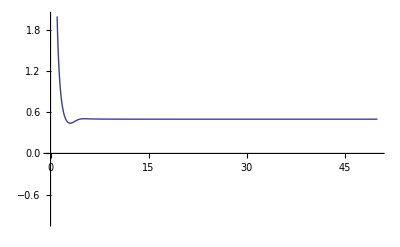

```mathematica
ListPlot[Transpose[{RawVEff[[1]],RawVEff[[2]]}],Joined->True,PlotTheme->None,PlotRange->{-1,2}]
```

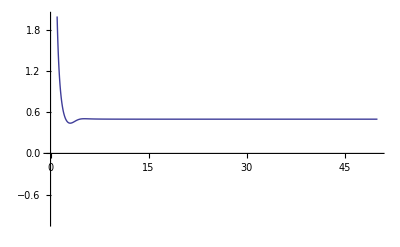

```mathematica
Plot[Veff0[R],{R,R1,R2},PlotTheme->None,PlotRange->{-1,2}]
```

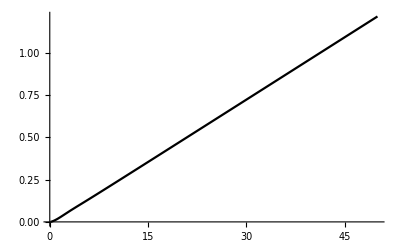

```mathematica
EE=1/2+0.000001;Fsol=NDSolve[{-1/(2mu)F''[R]+(Veff0[R]-EE)F[R]==0,F[R1]==0,F'[R1]==0.01},F[R],{R,R1,R2}];

Plot[F[R]/.Fsol,{R,R1,R2}]
```

```mathematica
Clear[A]
```

```mathematica
Solve[{Fa==A(Sin[k Ra]+td Cos[k Ra]),Fb==A(Sin[k Rb]+td Cos[k Rb])},{A,td}]
```

{{A→(Fb Cos[k Ra]-Fa Cos[k Rb])/(-Cos[k Rb] Sin[k Ra]+Cos[k Ra] Sin[k Rb]),td→(-Fb Sin[k Ra]+Fa Sin[k Rb])/(Fb Cos[k Ra]-Fa Cos[k Rb])}}

```mathematica
SingleChannelPhase[EE_,mu_,V_,R1_,R2_,Eth_]:=Module[{td, k,Fsol,F,R,Fa,Fb,Ra,Rb,ascat,delta},
k=√(2 mu(EE-Eth));
Fsol=NDSolve[{-1/(2mu)F''[R]+(Veff0[R]-EE)F[R]==0,F[R1]==0,F'[R1]==0.01},F[R],{R,R1,R2}];
Ra=0.9 R2;
Rb=0.99R2;
Fa=F[R]/.Fsol[[1]]/.R->Ra;
Fb=F[R]/.Fsol[[1]]/.R->Rb;
td=(-Fb Sin[k Ra]+Fa Sin[k Rb])/(Fb Cos[k Ra]-Fa Cos[k Rb]);
ascat=-td/k;
delta=ArcTan[td];
{ascat,delta}
]
```

```mathematica
scatlendata=Table[{EE,SingleChannelPhase[1/2+EE,mu,Veff0,R1,R2,1/2][[1]]},{EE,0.01,0.98,0.01}];
```

```mathematica
Phaseshiftdata=Table[{EE,SingleChannelPhase[1/2+EE,mu,Veff0,R1,R2,1/2][[2]]},{EE,0.01,0.98,0.01}];
```

```mathematica
Fortran1chanData=Transpose[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/Observables.1chan.dat"]];
Fortran1chanphaseshift=Transpose[{Fortran1chanData[[1]],Fortran1chanData[[3]]}];
Fortran1chanScatLen=Transpose[{Fortran1chanData[[1]],Fortran1chanData[[2]]}];
```

```mathematica
Fortran4chanData=Transpose[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/Observables.dat"]];
Fortran4chanScatLen=Transpose[{Fortran4chanData[[1]],Fortran4chanData[[2]]}];
```

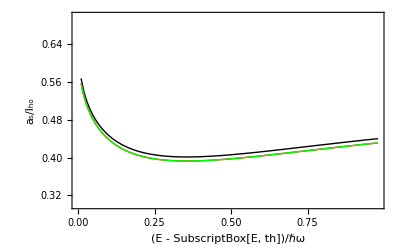

```mathematica
ListPlot[{scatlendata,Fortran1chanScatLen,Fortran4chanScatLen},Joined->True,PlotTheme->None,Frame->True,FrameLabel->{"(E - SubscriptBox[E, th])/ℏω","a_s/l_ho"},PlotStyle->{Black,Red,Green},PlotRange->{0.3,0.7}]
```

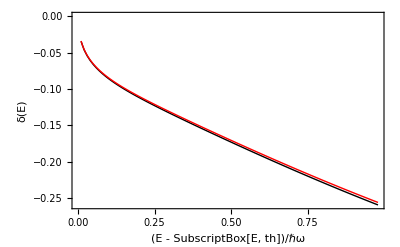

```mathematica
ListPlot[{Phaseshiftdata,Fortran1chanphaseshift},Joined->True,PlotTheme->None,Frame->True,FrameLabel->{"(E - SubscriptBox[E, th])/ℏω","δ(E)"},PlotStyle->{Black,Red}]
```